```mathematica
speedupData = Drop[Import["\\\\wsl.localhost\\Ubuntu\\home\\toler\\projects\\CGAL_curvature\\mathematica_tests\\data_files\\performance_data\\speedups.csv","Data"],1];
neighborNums = Table[speedupData[[i,1]],{i,Length[speedupData]}];
performanceRatios =Table[speedupData[[i,2]],{i,Length[speedupData]}];
treeTimes = Table[speedupData[[i,3]],{i,Length[speedupData]}];
prVnn =  Table[{neighborNums[[i]],performanceRatios[[i]]},{i,Length[neighborNums]}];
ttVnn =  Table[{neighborNums[[i]],treeTimes[[i]]},{i,Length[neighborNums]}];
```

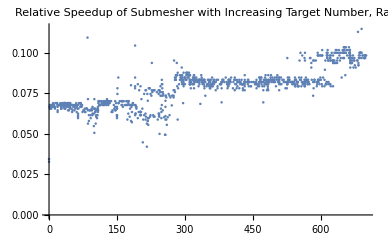

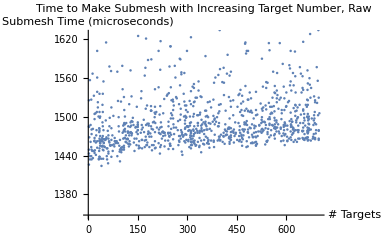

```mathematica
ListPlot[prVnn,PlotLabel->"Relative Speedup of Submesher with Increasing Target Number, Raw"]
ListPlot[ttVnn, PlotLabel->"Time to Make Submesh with Increasing Target Number, Raw",AxesLabel->{"# Targets","Submesh Time (microseconds)"}]
```

```mathematica
binnedprVnn = GatherBy[prVnn, First];
binnedttVnn = GatherBy[ttVnn,First];
averagesprVnn = Table[Mean[Table[binnedprVnn[[i,j]],{j,Length[binnedprVnn[[i]]]}]],{i,Length[binnedprVnn]}];
averagesttVnn= Table[Mean[Table[binnedttVnn[[i,j]],{j,Length[binnedprVnn[[i]]]}]],{i,Length[binnedprVnn]}];
```

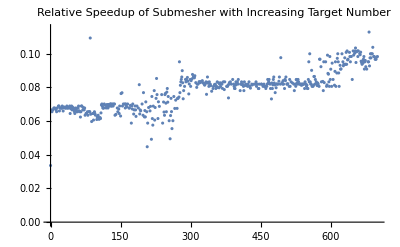

```mathematica
ListPlot[averagesprVnn,PlotLabel->"Relative Speedup of Submesher with Increasing Target Number"]
ListPlot[averagesttVnn, PlotLabel->"Time to Make Submesh with Increasing Target Number",AxesLabel->{"# Targets","Submesh Time (microseconds)"}]
```